```mathematica
Lecture 11: Differential  Equations
```

Key functions include:

```mathematica
{DSolve,NDSolve,LaplaceTransform}
```

## Ordinary differential equations

### Exercise Subsection

Solve the differential equation -y[x]+y'[x]+y''[x]==x with the initial condition y[0]==0, y'[0]==1.

```mathematica
y[x]/.First@DSolve[{-y[x]+y'[x]+y''[x]==x,y[0]==0,y'[0]==1},y,x]
```

1/2 (-2+ⅇ^((-1/2-(√5)/2) x)-√5 ⅇ^((-1/2-(√5)/2) x)+ⅇ^((-1/2+(√5)/2) x)+√5 ⅇ^((-1/2+(√5)/2) x)-2 x)

### Exercise Subsection

The spread of a disease in a population is modeled by the differential equation in the next cell

```mathematica
P'[t]==-b P[t]+a (1-P[t]) P[t]
```

where P[t] is the percentage of the population with the disease at time t and a and b are constants with 0 < a < b.  

Solve for P[t] and then show that limit of P[t] as t approaches infinity is equal to 0.  

If P[0] = .75, a = 1, and b = 1.1, at what time t will P[t] = .1?

```mathematica
f[t_]:=Evaluate[P[t]/.First@DSolve[{P'[t]==-b P[t]+a(1-P[t])P[t],P[0]==.75},P,t]/.{a->1,b->1.1}//Chop]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
f[t]
```

-(0.1 ⅇ^(-1.37679+t))/(ⅇ^(-1.37679+t)-ⅇ^(-1.25163+1.1 t))

```mathematica
Solve[f[t]==.1,t]//Quiet//Chop//First
```

{t→5.67984}

### Exercise Subsection

The slope field for a first order differential equation of the form y'[x] == f[x,y] is the vector field Normalize@{1,f[x,y]}.   

a. Plot the slope field for the differential equation y'[x] == y[x]+x^2 for values of x and y between -2 and 2, using these options in the VectorPlot function: VectorStyle->Arrowheads[0], VectorColorFunction->(Gray&), VectorScale->.01,
VectorPoints->40.

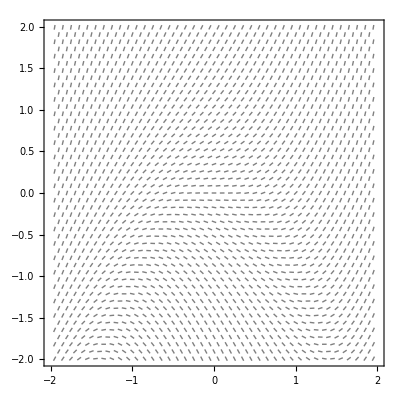

```mathematica
G1=VectorPlot[Normalize@{1,y+x^2},{x,-2,2},{y,-2,2},VectorStyle->Arrowheads[0],VectorColorFunction->(Gray&),VectorScale->.01,VectorPoints->40]
```

b. Solve the differential equation y'[x] == y[x]+x^2 with the initial condition y[0]==a.  Then plot the solutions for values of a in the list {-2,-1,0,1,2} on top of the plot of the slope field in part a.

```mathematica
f[x_,a_]:=Evaluate[y[x]/.First@DSolve[{y'[x]== y[x]+x^2,y[0]==a},y,x]]
```

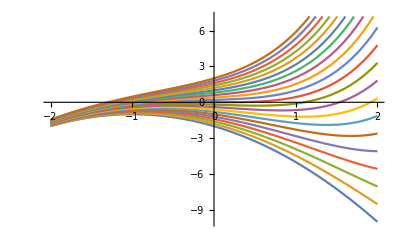

```mathematica
G2=Plot[Evaluate@Table[f[x,a],{a,-2,2,1/5}],{x,-2,2}]
```

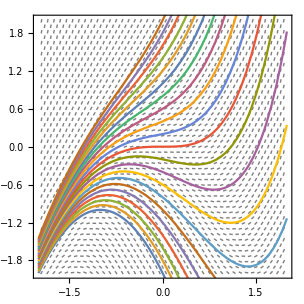

```mathematica
Show[G1,G2]
```

### Exercise Subsection

Solve the differential equation y’’[x] ==x y[x]+1 with initial conditions y[0]==1, y’[0]==1.  The solution will be a bit nasty, so use N and Series to find a degree 10 polynomial that best approximates the solution near x = 0.

```mathematica
f[x_]:=Evaluate[y[x]/.First@DSolve[{y''[x]==x y[x]+1,y[0]==1,y'[0]==1},y,x]]
```

```mathematica
Series[f[x],{x,0,10}]//N
```

1.+(x+0.)+0.5 (x+0.)^2+0.166667 (x+0.)^3+0.0833333 (x+0.)^4+0.025 (x+0.)^5+0.00555556 (x+0.)^6+0.00198413 (x+0.)^7+0.000446429 (x+0.)^8+0.0000771605 (x+0.)^9+0.0000220459 (x+0.)^10+O[x+0.]^11

## Parameterized differential equations

### Exercise Subsection

Some differential equations (like Sturm-Liouville problems, see https://en.wikipedia.org/wiki/Sturm%E2%80%93Liouville_theory ) can involve a parameter λ.  The goal is to find the values of λ that give nonzero solutions and then to find those solutions.  For example, consider the following differential equation with boundary conditions:

```mathematica
conditions=DSolve[{y''[x]+λ y[x]==0,y'[0]==0,y[π]==0},y[x],x]
```

{{y[x]→Piecewise[{{C[1] Cos[x √λ], n∈ℤ&&n≥1&&λ==(-1/2+n)^2}, {0, True}}]}}

```mathematica
Simplify[y[x]/.First@conditions/.{λ->(-1/2+n)^2,C[1]->1},n∈Integers&&n≥1]/.{n->n}
```

Cos[(-1/2+n) x]

a. Create a list named solutions of solutions to the above differential equation for the smallest 8 values for λ that give nonzero solutions, taking C[1] to be 1.  Plot this list on the interval from 0 to π.

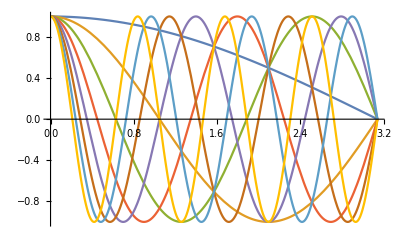

```mathematica
Plot[Evaluate@Table[Cos[(-1/2+n) x],{n,1,8}],{x,0,π}]
```

b. Show that the integral of the product of two different solutions in solutions on the interval from 0 to π is equal to 0.

### Exercise Subsection

Solve the integral equation

```mathematica
equation=y[x]==x^3+λ∫_0^x (t- x)y[t]ⅆt;
```

using DSolve, and then Plot sample solutions for various values of λ, fixing the PlotRange option to better understand how the solutions change as λ varies.

## Partial differential equations

### Exercise Subsection

While general solutions to ordinary differential equations involve arbitrary constants, general solutions to partial differential equations involve arbitrary functions.

Solve the differential equation in the next cell, and then replace the arbitrary function C[1] with a function (such as Sin) and then plot the resulting solution in R^3.

```mathematica
SamplePDE=D[u[x,y],x]-D[u[x,y],y]==(-2x u[x,y])
```

-u^(0,1)[x,y]+u^(1,0)[x,y]==-2 x u[x,y]

```mathematica
f[x_,y_]:=Evaluate[u[x,y]/.First@DSolve[SamplePDE,u[x,y],{x,y}]/.{C[1]->Sin}]
```

```mathematica
Plot3D[f[x,y],{x,-π,π},{y,-π,π},PlotRange->All]
```

-Graphics3D-

### Exercise Subsection

The one dimensional wave equation models wave motion in a vibrating string.  The one dimensional wave equation is the partial differential equation given in the next cell

```mathematica
wave=D[u[t,x],{t,2}]==D[u[t,x],{x,2}];
```

Use DSolve to find the solution to the wave equation together with the conditions in the next cell

```mathematica
conditions={u[0,x]==Exp[-x^2],Derivative[1,0][u][0,x]==0};
```

These conditions model a taut string being plucked and the resulting waves propagating in two directions. Use Manipulate on the variable t to understand what happens to the Plot of the solution u[t,x] for values of x between -10 and 10.

```mathematica
f[t_,x_]:=Evaluate[u[t,x]/.First@DSolve[{wave,conditions},u[t,x],{t,x}]]
```

```mathematica
Manipulate[Plot[f[t,x],{x,-10,10},PlotRange->{0,1}],{t,0,10}]
```

## Systems of differential equations

### Exercise Subsection

Use DSolve to solve the system of differential equations in the next cell and then plot the resulting parametric equations {x[t],y[t]} as t ranges from -2 π to 2 π.  What is the ArcLength of this curve?

```mathematica
system={x'[t]==Cos[t^2/2],y'[t]==Sin[t^2/2],x[0]==0,y[0]==0};
```

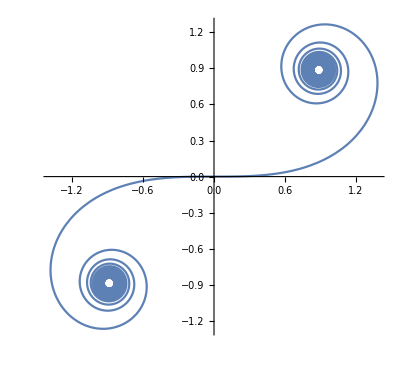

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.First@DSolve[system,{x[t],y[t]},t]],{t,-7π,7π}]
```

### Exercise Subsection

The Lotka-Volterra equations model a system of prey and predators (like the interdependent  populations of rabbits and wolves).  The equations in the cell below give one example of a Lotka-Volterra system where x[t] models the population of prey at time t and y[t] is the population of predators at time t.

```mathematica
LVequations={x'[t]==2x[t]-x[t] y[t],y'[t]==-y[t]+1/3 x[t] y[t],x[0]==2,y[0]==1};
```

Use NDSolve to numerically solve this differential equation for {x,y} on the range {t,0,20}.  Then Plot the graphs of x[t] and y[t] on the same axis as t ranges from 0 to 20.  Then use ParametricPlot to show the curve {x[t],y[t]} as t ranges from 0 to 20.

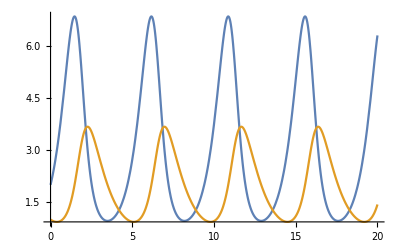

```mathematica
Plot[Evaluate[{x[t],y[t]}/.First@NDSolve[LVequations,{x[t],y[t]},{t,0,20}]],{t,0,20}]
```

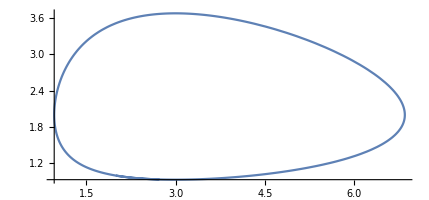

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.First@NDSolve[LVequations,{x[t],y[t]},{t,0,20}]],{t,0,5}]
```

### Exercise Subsection

Some linear systems can be written as a matrix multiplication of the form x’ == A.x where x is a vector of unknown functions in R^n and A is a nxn matrix that may contain functions of t.  An example of the syntax to solve such a system using DSolve is shown below:

```mathematica
A={{1,2},{-1,0}};
Clear[f]
f[t]=Evaluate[x[t]/.First@DSolve[{x'[t]==A.x[t],x[0]=={1,1}},Element[x[t],Vectors[2]],t]];
```

```mathematica
f[t]
```

{1/7 ⅇ^(t/2) (7 Cos[(√7 t)/2]+5 √7 Sin[(√7 t)/2]),-1/7 ⅇ^(t/2) (-7 Cos[(√7 t)/2]+3 √7 Sin[(√7 t)/2])}

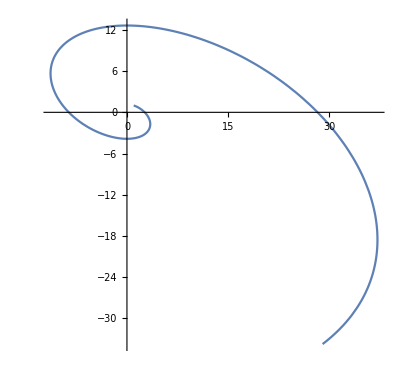

```mathematica
ParametricPlot[Evaluate@f[t],{t,0,2Pi}]
```

Use ParametricPlot to plot the solution curve f[t] (it will help to use Evaluate) to the above linear system.  Then solve and plot the solution to the same system when the matrix A is changed to each of the following:

```mathematica
A={{0,4},{-1,0}};
A={{1,4},{-4,1}};
A={{Sin[t]/(√2),-Cos[t]-Sin[t]/(√2)},{Cos[t]+Sin[t]/(√2),Sin[t]/(√2)}};
```

### Exercise Subsection

A mass m_1 is placed on a rigid swinging rod of length L_1 attached to the ceiling, a mass m_2 is attached to a rigid swinging rod of length L_2 attached to the first mass.  Gravity is g and the overall friction in the system is f.  Then the first mass is moved to an angle θ_1, the second mass is moved to an angle θ_2, and the system is released freely.  The swinging of each mass affects the other, creating an interdependent system of differential equations.  This system is solved below and visualized:

```mathematica
{Subscript[m, 1],Subscript[m, 2],Subscript[L, 1],Subscript[L, 2],g,f,Subscript[θ, 1],Subscript[θ, 2]}={4,4,1,1,9.81,0,Pi/4,0};
A=({{0, 1, 0, 0}, {(-g(Subscript[m, 1]+Subscript[m, 2]))/(Subscript[L, 1] Subscript[m, 1]), -f, (g Subscript[m, 2])/(Subscript[L, 1] Subscript[m, 1]), 0}, {0, 0, 0, 1}, {(g (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[L, 2] Subscript[m, 1]), 0, -(g (Subscript[m, 1]+Subscript[m, 2]))/(Subscript[L, 2] Subscript[m, 1]), -f}});
{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4]}=x[t]/.First@DSolve[{x'[t]==A.x[t],x[0]=={Subscript[θ, 1],0,0,0}},Element[x[t],Vectors[4]],t];

{a,b}={{Subscript[L, 1] Sin[Subscript[x, 1]],-Subscript[L, 1]Cos[Subscript[x, 1]]},{Subscript[L, 1] Sin[Subscript[x, 1]]+Subscript[L, 2] Sin[Subscript[x, 3]],-Subscript[L, 1]Cos[Subscript[x, 1]]-Subscript[L, 2] Cos[Subscript[x, 3]]}};

Manipulate[Show[
ParametricPlot[{a,b},{t,0,n},PlotRange->{{-2,2},{-3,0}}],
Graphics[{Line[{{0,0},a,b}],Blue,Disk[a,.025 √Subscript[m, 1]],Red,Disk[b,.025 √Subscript[m, 2]]}]/.{t->n}],
{n,0.001,15}]
```

## Laplace transforms

### Exercise Subsection

The LaplaceTransform is an integral transform that can change a differential equation in the variable t into an algebraic equation in the variable s.  The method to solve a differential equation in is as follows:

1. Take the LaplaceTransform on both sides of the equation.
2. Solve the new equation for the LaplaceTransorm of y.
3. Take the InverseLaplaceTransform to get the final solution.  

Use this method to solve the differential equation in the next cell.

```mathematica
equation=y'''[t]+y'[t]==-Cos[t]+1/(1+t^2);
```

```mathematica
Clear[f]
```

```mathematica
f[t_]:=Evaluate@InverseLaplaceTransform[LaplaceTransform[y[t],t,s]/.First@Solve[LaplaceTransform[equation,t,s],LaplaceTransform[y[t],t,s]],s,t]
```

Use the LaplaceTransform to solve the following system of differential equations.

```mathematica
system={x'[t]==x[t]+y[t]+Exp[-t],y'[t]==-x[t]+2y[t]};
```